```mathematica
ClearAll["Global`*"]

(* Consider the metric,
ds^2 = w^2 Cosh^2[Log[w/c1] + k (y- c2)] Subscript[g, μν] dx^μ dx^ν - dy^2
we convert y -> z by the following transformations representing the metric in conformal coordinates:
*)

Solve[Integrate[1/(w Cosh[Log[w/c1] + k (y- c2)]),y] == z,y,Reals](*y in terms of conformal coordinate z*)
```

{{y→ConditionalExpression[(c2 k-ArcSinh[Cot[k w z]]-Log[w/c1])/k, ]}}

```mathematica
(w Cosh[Log[w/c1] + k (y- c2)])^2 /. y-> (c2 k-ArcSinh[Cot[k w z]]-Log[w/c1])/k// FullSimplify (*For (0 < z ≤ π/(2 k w) & c1 > 0 & k > 0 & w>  0 ), reproducing eqn(10)*)
```

w^2 Csc[k w z]^2

```mathematica
(*The warp factor in conformal coordinates, Reff eqn(10)*)
Zp = 1/(w Csc[k w z]); (*0 < z ≤ π/(2 k w)*)

eqn5 = D[1/Zp D[V[z],z],z] + q^2/Zp V[z] == 0; (*   Rho meson EOM, Reff eqn(18),
whose solution can be obtained analytically under a change of variables shown below,
*)

Dsol = DSolveChangeVariables[Inactive[DSolve][eqn5,V[z],z],V1,t,t==k w z];
Activate[Dsol]
```

{{V1[t]→C[1] Hypergeometric2F1[-1/4-(√(4 k^2 q^2 w^2+k^4 w^4))/(4 k^2 w^2),-1/4+(√(4 k^2 q^2 w^2+k^4 w^4))/(4 k^2 w^2),1/2,Cos[t]^2]+ⅈ C[2] Cos[t] Hypergeometric2F1[1/4-(√(4 k^2 q^2 w^2+k^4 w^4))/(4 k^2 w^2),1/4+(√(4 k^2 q^2 w^2+k^4 w^4))/(4 k^2 w^2),3/2,Cos[t]^2]}}

```mathematica
(*Analytical solution of RHO meson EOM with integral constants chosen as Nphi and bphi*)

sol[z_] = Nphi(Hypergeometric2F1[-1/4-(√(4 k^2 q^2 w^2+k^4 w^4))/(4 k^2 w^2),-1/4+(√(4 k^2 q^2 w^2+k^4 w^4))/(4 k^2 w^2),1/2,Cos[k w z]^2]+bphi  Cos[k w z] Hypergeometric2F1[1/4-(√(4 k^2 q^2 w^2+k^4 w^4))/(4 k^2 w^2),1/4+(√(4 k^2 q^2 w^2+k^4 w^4))/(4 k^2 w^2),3/2,Cos[k w z]^2]); 

(* Now we apply the Boundary conditions given to the equation of motion*)

bphi1 = bphi /.Solve[sol[ϵ] == 0,bphi][[1]] // Simplify;

Vp = D[sol[z],z] /. z-> zm;

bphi2 = bphi /.Solve[Vp==0,bphi][[1]] // Simplify;

(*Since bphi is an integral constant, to satisfy the boundary conditions we need bphi1 = bphi2 leading to the expression below.*)

expr = Numerator[bphi1]Denominator[bphi2] - Numerator[bphi2] Denominator[bphi1];
```

```mathematica
k = 10000;         (*Chosen for now*)
ϵ = 10^-15;           (*Numerical approximation for ϵ -> 0 *)
g52 = (4 Pi^2)/k;      (*5-D gauge coupling, reffer eqn(22), with Nc = 3*)
q=77526/100; (*Mass of Rho(770)*)

zms = 1/Range[323 ,348,1]; (* range of values for the position of IR *)

(*Fixing the rho mass with q = 775.26, we get a constraint between ω and zm.*)

wvals = Table[Block[{zm = zms[[i]]},
w/.FindRoot[expr,{w,1/100,Pi/(2 k zm)},WorkingPrecision->50]
],{i,1,Length[zms]}];  (*Returns a list of ω values corresponding to values in zms*)
```

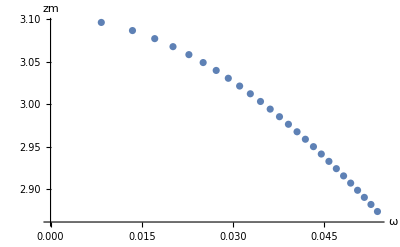

```mathematica
ListPlot[Transpose[
{wvals,zms 1000} (* 1000 is multiplied to convert Mev^-1 to Gev^-1, (variable is not modified)*)
],
AxesLabel->{"ω","zm"}
] (*Ploting the relation between ω and zm, reffer Figure 2*)
```

```mathematica
Reduce[0 < z <= Pi/(2 k w),w] /. z-> zms[[-1]] //N  (*constraint on w from the warp factor, we can easily check for different values of zm by replaing the index*)
```

0.<w≤0.0546637

```mathematica
(*We have estimated bphi above, Now we find Nphi by using the orthonormality condition numerically*)

Nk = ParallelTable[Block[{bphi = bphi1,Nphi=1,zm = zms[[i]],w = wvals[[i]]},
1/Sqrt[NIntegrate[1/Zp sol[z]^2,{z,ϵ ,zm},WorkingPrecision->20]]
],{i , 1 , Length[zms]}];    (*Returns a list of Nphi values corresponding to different values of zm*)
```

```mathematica
(*
Using the relation reff eqn(23), we can find Subscript[F, ρ]^(1/2);
*)

Frhos = Table[Block[{q = 77526/100,bphi = bphi1,Nphi = Nk[[i]],zm=zms[[i]],w = wvals[[i]]},
Sqrt[Sqrt[1/g52 (sol'[ϵ]/(k ϵ))^2]]
],{i,1,Length[zms]}]; (*Returns a list of Subscript[F, ρ]^(1/2) values corresponding to different values of zm*)
```

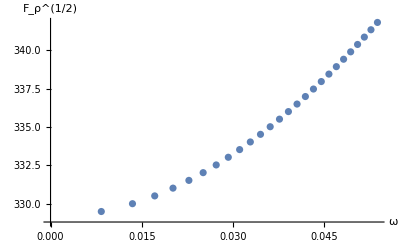

```mathematica
ListPlot[Transpose[
{wvals,Frhos} 
],
AxesLabel->{"ω","F_ρ^(1/2)"}
] (*Ploting the relation between ω and Subscript[F, ρ]^(1/2), refer Figure 3*)
```

```mathematica
Export[NotebookDirectory[]<>"zms.mx",zms]
Export[NotebookDirectory[]<>"wvals.mx",wvals]
Export[NotebookDirectory[]<>"Frhos.mx",Frhos]
```

C:\Users\Nabeel Thahir\Desktop\Major Project\Publication Code\Model A\zms.mx

C:\Users\Nabeel Thahir\Desktop\Major Project\Publication Code\Model A\wvals.mx

C:\Users\Nabeel Thahir\Desktop\Major Project\Publication Code\Model A\Frhos.mx